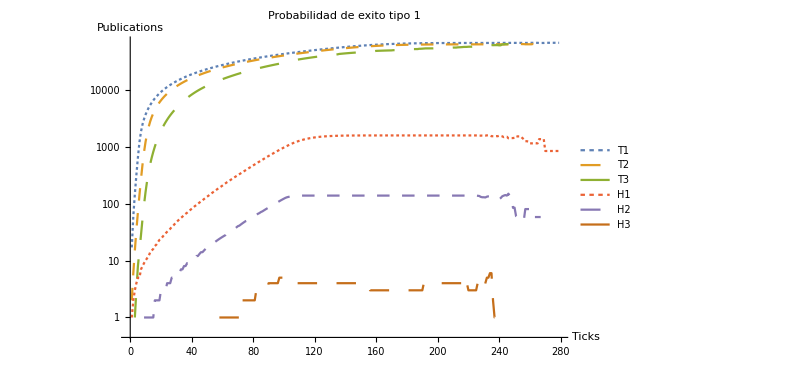
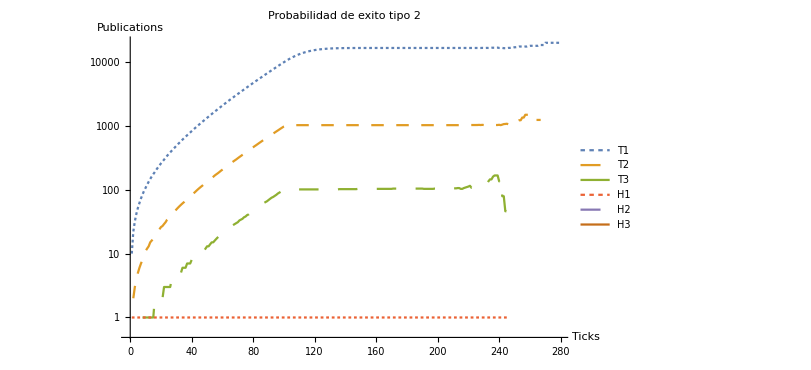
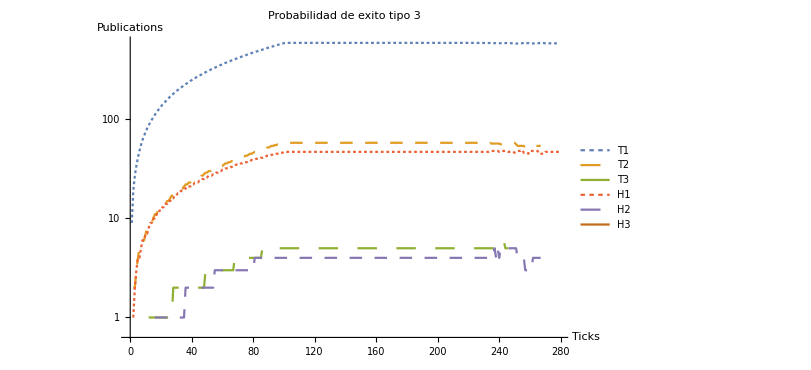
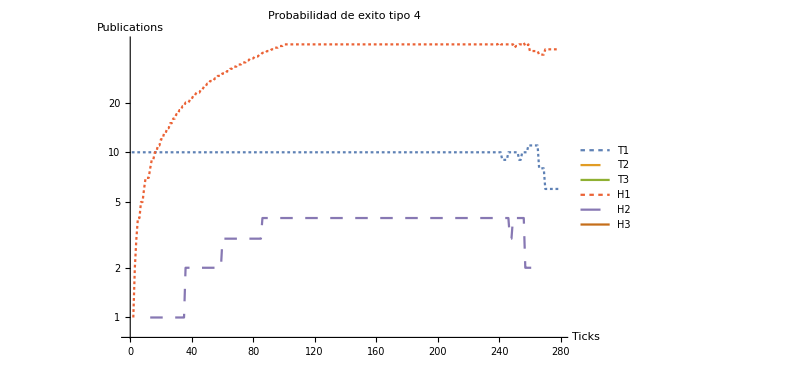
-Graphics- | -Graphics-
-Graphics- | -Graphics-

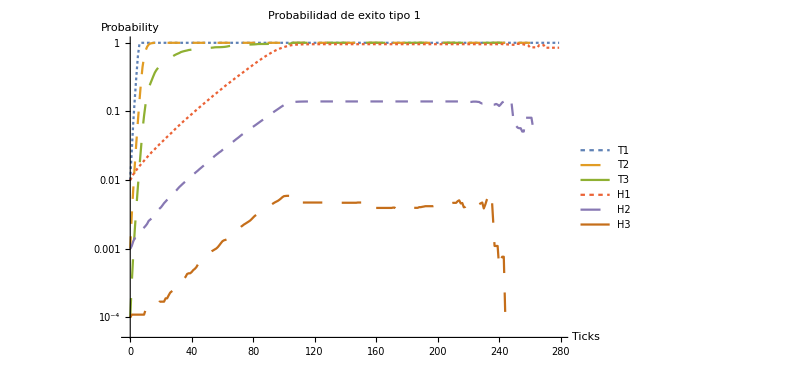
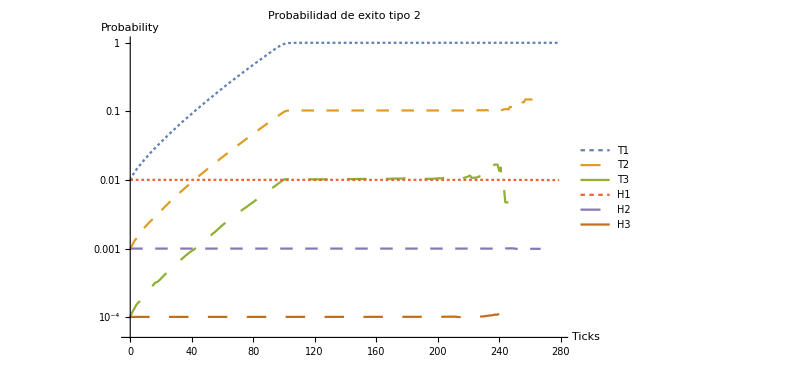
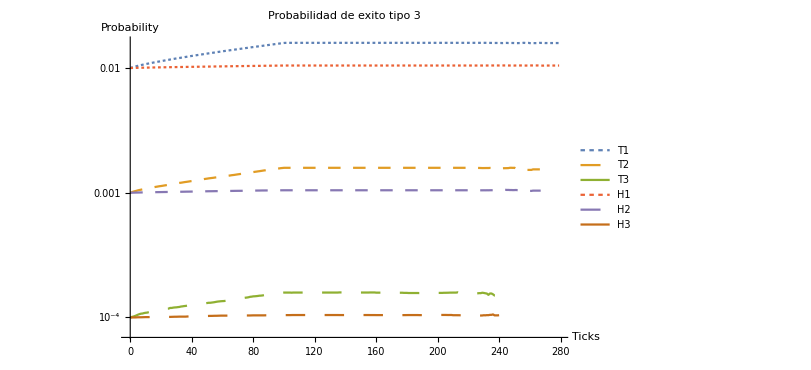
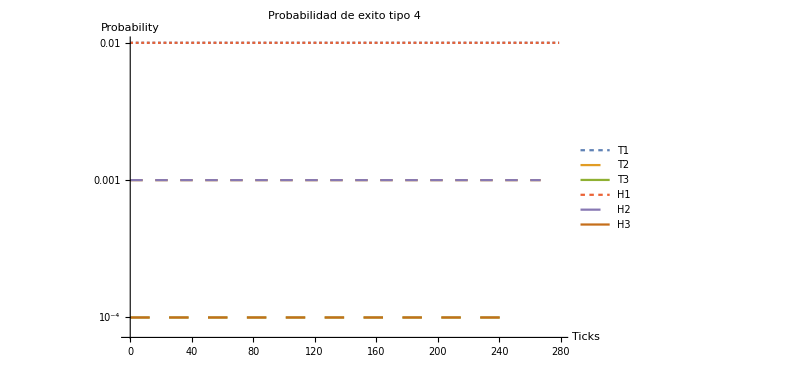
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory[y<>"/images"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18}];
pub1= Import[y<>"/averageResults/pub1-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/pub1-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/pub1-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/pub5-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/pub5-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/pub5-1.0E-4-100-true-curve.csv"];
plotPub1 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 1",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];

Export["pub-1-100-true.png",plotPub1];

pub1= Import[y<>"/averageResults/pub2-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/pub2-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/pub2-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/pub6-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/pub6-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/pub6-1.0E-4-100-true-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 2", PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-2-100-true.png",plotPub2];

pub1= Import[y<>"/averageResults/pub3-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/pub3-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/pub3-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/pub7-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/pub7-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/pub7-1.0E-4-100-true-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 3",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-3-100-true.png",plotPub3];

pub1= Import[y<>"/averageResults/pub4-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/pub4-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/pub4-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/pub8-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/pub8-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/pub8-1.0E-4-100-true-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 4",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-4-100-true.png",plotPub4];

pub1= Import[y<>"/averageResults/prob1-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob1-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob1-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob5-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob5-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob5-1.0E-4-100-true-curve.csv"];
plotProb1 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All, PlotLabel-> "Probabilidad de exito tipo 1",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];

Export["prob-1-100-true.png",plotPub5];

pub1= Import[y<>"/averageResults/prob2-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob2-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob2-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob6-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob6-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob6-1.0E-4-100-true-curve.csv"];
plotProb2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All, PlotLabel-> "Probabilidad de exito tipo 2",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-2-100-true.png",plotPub6];

pub1= Import[y<>"/averageResults/prob3-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob3-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob3-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob7-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob7-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob7-1.0E-4-100-true-curve.csv"];
plotProb3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 3",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-3-100-true.png",plotPub];

pub1= Import[y<>"/averageResults/prob4-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob4-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob4-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob8-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob8-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob8-1.0E-4-100-true-curve.csv"];
plotProb4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Ticks","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All, PlotLabel-> "Probabilidad de exito tipo 4",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-4-100-true.png",plotPub];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["pub-total-100-true.png",pubTotal];
probTotal=Grid[{{plotProb1,plotProb2},{plotProb3,plotProb4}}]
Export["prob-total-100-true.png",probTotal];
```